```mathematica
at[k_,t_]:=1/k Sum[MoebiusMu[k/d] t^d,{d,Divisors[k]}]
atf[k_,s_]:=1/k Sum[MoebiusMu[k/d] PrimeZetaP[d s],{d,Divisors[k]}]
```

```mathematica
N@Sum[Log[1/(1-Prime[p]^-s)],{p,1,1000}]/.s->2
```

0.497688

```mathematica
Log[Zeta[3.]]
```

0.184034

```mathematica
bex[x_,r_,s_]:=Sum[at[k,Prime[p]^-s] HarmonicNumber[Floor[x/k]],{k,1,x},{p,1,r}]
bex2[x_,r_,s_]:=Sum[HarmonicNumber[Floor[x/k]]Sum[at[k,Prime[p]^-s] ,{p,1,r}],{k,1,x}]
pla[k_,r_,s_]:=Sum[at[k,Prime[p]^-s] ,{p,1,r}]
```

```mathematica
N@bex[100,100,3]
```

0.184034

```mathematica
N@bex2[100,100,3]
```

0.184034

```mathematica
pla[10,Infinity,s]
```

1/10 (PrimeZetaP[s]-PrimeZetaP[2 s]-PrimeZetaP[5 s]+PrimeZetaP[10 s])

```mathematica
1/5 (-PrimeZetaP[s]+PrimeZetaP[5 s])/.s->2
```

1/5 (-PrimeZetaP[2]+PrimeZetaP[10])

```mathematica
atf[10,s]
```

1/10 (PrimeZetaP[s]-PrimeZetaP[2 s]-PrimeZetaP[5 s]+PrimeZetaP[10 s])

```mathematica
sef[x_,s_]:=Sum[atf[k,s]HarmonicNumber[Floor[x/k]],{k,1,x}]
```

```mathematica
Limit[N@sef[2,s],s->2]
```

0.490744

```mathematica
kk[n_]:=kk[n]=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
```

```mathematica
N@Sum[kk[k]/k^s,{k,1,10}]/.s->0
```

5.33333

```mathematica
bex4[x_,s_]:=Sum[at[k,Prime[p]^-s] HarmonicNumber[Floor[1/k Log[Prime[p],x]]],{k,1,x},{p,1,PrimePi[x]}]
```

```mathematica
N@bex4[10,0]
```

5.33333

```mathematica
b1[x_,t_]:=Sum[t^k/k,{k,1,x}]
b2[x_,t_]:=Sum[at[k,t]HarmonicNumber[Floor[x/k]],{k,1,x}]
```

```mathematica
N@Sum[b1[10,t]/.t->Prime[p]^-s,{p,1,100}]/.s->2
```

0.497446

```mathematica
N@Sum[Expand[b2[10,t]]/.t->Prime[p]^-s,{p,1,100}]/.s->2
```

0.497446

```mathematica
PrimePi[10]
```

4

```mathematica
atf[k_,s_]:=1/k Sum[MoebiusMu[k/d] PrimeZetaP[d s],{d,Divisors[k]}]
```

```mathematica
N[Sum[atf[k,s],{k,1,1000}]Log[Zeta[1+t]]/.s->2/.t->.0001]
```

0.0156273

```mathematica
Sum[atf[k,s] HarmonicNumber[x/k],{k,1,10000}]/.x->100000./.s->3
```

0.183001

```mathematica
Log[Zeta[3.]]
```

0.184034

```mathematica
N@Product[Floor[x/k]^atf[k,s],{k,1,1000}]/.x->10000./.s->3
```

1.20394

```mathematica
Zeta[3.]
```

1.20206

```mathematica
N@Product[Floor[x/k]^atf[k,s],{k,1,5000}]/.x->100000./.s->2
```

1.64657

```mathematica
Zeta[2.]
```

1.64493

```mathematica
N[Product[Floor[x/k]^atf[k,s],{k,1,5000}]/.x->100000./.s->.5+I]
```

0.142966-0.723293 ⅈ

```mathematica
Zeta[.5+I]
```

0.143936-0.7221 ⅈ

```mathematica
N[Product[x/k^atf[k,s],{k,1,5000}]/.x->100000./.s->.5+I]
```

1.4668025459927×10^24999-7.18646833959589×10^24999 ⅈ

```mathematica
N[Product[Floor[x/k]^atf[k,s],{k,1,5000}]/.x->100000./.s->.5+5I]
```

0.70295+0.230022 ⅈ

```mathematica
Zeta[.5+5I]
```

0.701812+0.231038 ⅈ

```mathematica
N[Product[Floor[x/k]^atf[k,s],{k,1,5000}]/.x->100000./.s->.5+14I]
```

0.0217977-0.102924 ⅈ

```mathematica
Zeta[.5+14I]
```

0.0222411-0.103258 ⅈ

```mathematica
N[Product[Floor[x/k]^atf[k,s],{k,1,5000}]/.x->100000./.s->N@ZetaZero[1]]
```

-4.96034×10^-15+2.14793×10^-15 ⅈ

```mathematica
Zeta[N@ZetaZero@1]
```

-5.32438×10^-15+2.34112×10^-15 ⅈ

```mathematica
Chop[-4.9603431715064615*^-15+2.1479321344984*^-15 ⅈ]
```

0

```mathematica
N[Product[Floor[x/k]^atf[k,s],{k,1,5000}]/.x->100000./.s->.5+30I]
```

-0.123471-0.580626 ⅈ

```mathematica
Zeta[.5+30I]
```

-0.120642-0.583691 ⅈ

```mathematica
N[Product[Floor[x/k]^atf[k,s],{k,1,5000}]/.x->100000./.s->N@ZetaZero[10]]
```

-1.42972×10^-14-1.30239×10^-14 ⅈ

```mathematica
Chop@N[Table[Floor[x/k]^atf[k,s],{k,1,10}]/.x->100000./.s->N@ZetaZero[1]]
```

{0,-1.44888×10^79+1.46307×10^79 ⅈ,-3.37656×10^49-1.22887×10^49 ⅈ,0.188104+0.0284527 ⅈ,1.75258×10^28+2.42162×10^28 ⅈ,0,-3.64522×10^19+2.88121×10^19 ⅈ,0.875965+0.191102 ⅈ,1.25199-0.279789 ⅈ,0}

```mathematica
Chop@N[Table[Floor[x/k]^atf[k,s],{k,1,10}]/.x->100000./.s->.5+10I]
```

{285.843-476.219 ⅈ,0.0704342-0.000901218 ⅈ,-0.073481+0.0221893 ⅈ,0.165696+0.623014 ⅈ,0.178221-0.154274 ⅈ,-2.33385+0.632036 ⅈ,0.401227-0.235033 ⅈ,1.14891+0.343913 ⅈ,1.06264+0.694619 ⅈ,1.06271+1.57616 ⅈ}

```mathematica
Chop@N[Table[Floor[x/k]^atf[k,s],{k,1,10}]/.x->100000./.s->N@ZetaZero[3]]
```

{0,-4.77624×10^73-2.45934×10^74 ⅈ,5.28424×10^48-5.49532×10^48 ⅈ,-0.357143-7.61561 ⅈ,7.75412×10^27+2.21134×10^27 ⅈ,0,-2.51751×10^18+1.43054×10^19 ⅈ,0.923573+0.00484855 ⅈ,0.735975+0.562404 ⅈ,0}

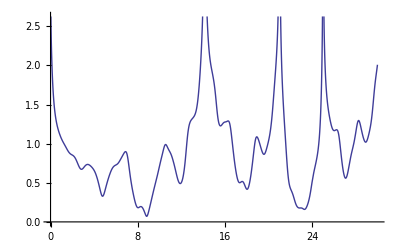

```mathematica
Plot[N@Abs[atf[1,.5+x I]],{x,0,30}]
```

```mathematica
x^atf[1,.001+ZetaZero[1]]/.x->1000.
```

-4.83071×10^-24+5.14195×10^-23 ⅈ

```mathematica
atf[1,ZetaZero[1]]
```

```mathematica
Table[N@PrimeZetaP[ZetaZero[k]],{k,100,120}]
```

{-29.8892+0.859491 ⅈ,-29.5703+2.1418 ⅈ,-30.5584-2.17752 ⅈ,-30.0378+3.32779 ⅈ,-29.658-1.29437 ⅈ,-30.9501+1.11501 ⅈ,-29.2616-4.67603 ⅈ,-30.1286+0.232038 ⅈ,-30.7131+1.05575 ⅈ,-29.1625-0.381546 ⅈ,-29.504-2.59282 ⅈ,-29.4799+1.02117 ⅈ,-29.9169-1.4293 ⅈ,-29.5656+0.392086 ⅈ,-29.3487+0.476 ⅈ,-28.7963+2.39194 ⅈ,-30.7325+2.05214 ⅈ,-29.801-0.331013 ⅈ,-29.6146+0.642008 ⅈ,-30.1543+0.287133 ⅈ,-30.917+0.446243 ⅈ}

```mathematica
N@ZetaZero[1]
```

0.5+14.1347 ⅈ

```mathematica
N[Product[Floor[x/k]^atf[k,s],{k,1,5000}]/.x->1000000./.s->.01+N@ZetaZero[10]]
```

0.012249+0.00634033 ⅈ

```mathematica
Zeta[ZetaZero[1]+.01]
```

0.00780232+0.00123556 ⅈ

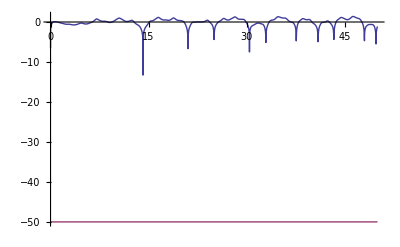

```mathematica
Plot[{N@Re[atf[1,.5+x I]], -35},{x,0,50}]
```

```mathematica
N[Product[Floor[x/k]^atf[k,s],{k,1,50}]/.x->10000./.s->2.]
```

1.56854

```mathematica
atf2[k_,s_]:=Sum[MoebiusMu[k/d]/k Sum[ MoebiusMu[j]/j f[d s j],{j,1,Infinity}],{d,Divisors[k]}]
atf3[k_,s_]:=Sum[MoebiusMu[k/d]/k  MoebiusMu[j]/j f[d s j],{d,Divisors[k]},{j,1,Infinity}]
atf3j[j_,k_,s_]:=Sum[MoebiusMu[k/d]/k  MoebiusMu[j]/j f[d s j],{d,Divisors[k]}]
```

```mathematica
FullSimplify[atf3j[j,12,s]]
```

((f[2 j s]-f[4 j s]-f[6 j s]+f[12 j s]) MoebiusMu[j])/(12 j)

```mathematica
Sum[atf[k,s]/k,{k,1,10000}]/.s->N@ZetaZero[1]
```

-20.0097+1.68081 ⅈ

```mathematica
Sum[atf[k,s]/k,{k,1,10000}]/.s->.1I+N@ZetaZero[1]
```

-1.61067+1.06435 ⅈ

```mathematica
Sum[(-1)^(k+1) Binomial[z-1,k]/k!/k,{k,1,Infinity}]
```

(-1+z) HypergeometricPFQ[{1,1,2-z},{2,2,2},1]

```mathematica
HarmonicNumber[10]
```

7381/2520

```mathematica
kk[n_]:=kk[n]=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
```

```mathematica
N@Sum[kk[k]/k^s,{k,1,10}]/.s->-1
```

26.1667

```mathematica
bex4[x_,s_]:=Sum[at[k,Prime[p]^-s] HarmonicNumber[Floor[1/k Log[Prime[p],x]]],{k,1,x},{p,1,PrimePi[x]}]
bex5[x_,s_]:=Sum[at[k,Prime[p]^-s] HarmonicNumber[Floor[1/k Log[Prime[p],x]]],{k,1,x},{p,1,PrimePi[x]}]
```

```mathematica
N@bex4[10,-1]
```

26.1667

```mathematica
N@bex5[10,-1]
```

26.1667

```mathematica
Product[E^((1/5)^k/k),{k,1,Infinity}]
```

5/4

```mathematica
Product[E^((1/3)^k/k),{k,1,Infinity}]
```

3/2

```mathematica
1/(1-1/5)
```

5/4

```mathematica
Product[(1/(1-t^k))^(s^j/j/t MoebiusMu[k]/k),{j,1,Infinity}]
```

(1-s)^(-(Log[1/(1-t^k)] MoebiusMu[k])/(k t))